# Forced precession under the near field torque

## Time scale estimation

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;
c=29979245800.0;
Ms=1.988409870698051*10^33;
km=10^5;
R=10*km;
M=1.4*Ms;
Is=2/5*M*R^2;
P=5;k=0.6;B=5*10^14;
ω=(2 π)/P;
ϵ=1*10^-7;
m=(B R^3)/2;
τc=(3 c^3 Is)/((2 m^2) ω^2)
τa=(2 R ω τc)/((3 k) c)
τp=N[P/ϵ]
τp/τa
ϵp=(3 B^2 R^5)/(20 (Is c^2))
```

4.55982×10^11

2.12371×10^7

5.×10^7

2.35438

3.74711×10^-8

```mathematica
ω^2*R^3/(G*1.4*Ms)
```

8.49924×10^-9

```mathematica
Solve[I1(1+ϵ)==I3&& (I3(I2-I1))/(I1(I3-I2))==δ,{I2,I3}]
```

{{I2→(I1 (1+δ) (1+ϵ))/(1+δ+ϵ),I3→I1 (1+ϵ)}}

```mathematica
Remove["Global`*"]
I1=I0;I2=I1 (1+ϵ1);I3=I1 (1+ϵ);
Ib=DiagonalMatrix[{I1,I2,I3}];
Ω={ω0*u1[t], ω0*u2[t], ω0*u3[t]};
p={m*Sin[χ]Cos[η],m Sin[χ]Sin[η],m Cos[χ]};
T1=(2 ω0^2*u[t]^2)/(3 c^3)Cross[Cross[Ω,p],p];
T2=k/(R c^2)Dot[Ω,p]*Cross[Ω,p];
```

## Triaxial case

```mathematica
Remove["Global`*"]
Ω={ω0*u1[t], ω0*u2[t], ω0*u3[t]};
p={m*Sin[χ]Cos[η],m Sin[χ]Sin[η],m Cos[χ]};
T2=Simplify[k/(R c^2)Dot[Ω,p]*Cross[Ω,p]/ω0/I0]
```

{1/(c^2 I0 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),-1/(c^2 I0 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]),1/(c^2 I0 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t])}

{{u1→InterpolatingFunction[…],u2→InterpolatingFunction[…],u3→InterpolatingFunction[…]}}

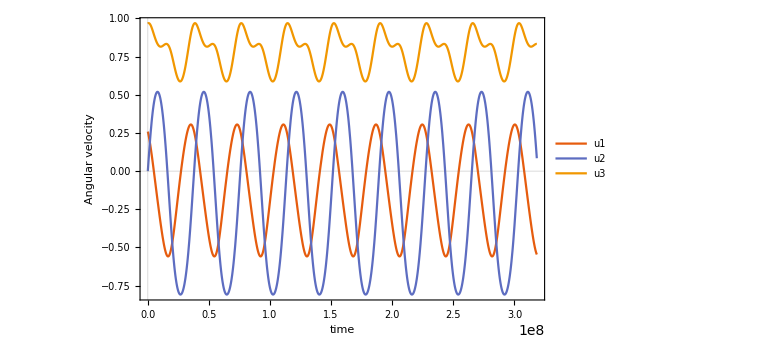

```mathematica
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=2;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=30.0/180*π;
θ=15/180.0*π;
τp=1/ω0/ϵ;

sol=Evaluate[Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ]]
Plot[Evaluate[{u1[t],u2[t],u3[t]}/.sol],{t,0,100*τp},PlotTheme->
"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White,PlotLegends->{"u1","u2","u3"}]
```

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=2;
B=8*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=InverseJacobiCN[Leff1/Sin[θ0eff],q];
```

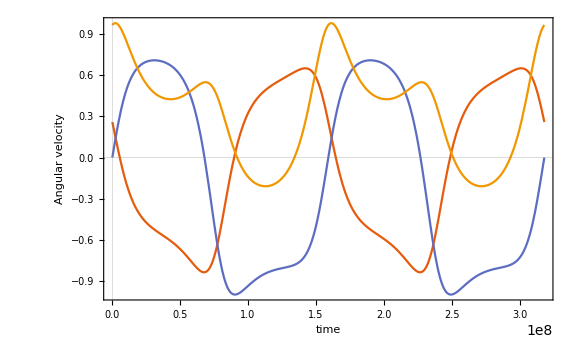

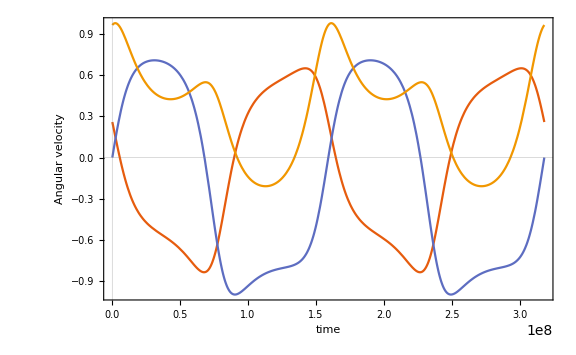

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
(*ϕ0=InverseJacobiSN[Leff2/Sin[θ0eff]/(1+δeff)^0.5,q];*)
(*ϕ0=InverseJacobiSN[Leff3/Cos[θ0eff],q];*)
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);

h=UnitStep[Ltol^2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q]*(e1eff.e1)+Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q]*(e2eff.e1)+Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e1),Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q]*(e1eff.e2)+Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q]*(e2eff.e2)+Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e2),Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q]*(e1eff.e3)+Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q]*(e2eff.e3)+Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e3)},h==0,sol={0,0,0}];{sol}]
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=5;
B=8*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
ϵeff=(Ieff3-Ieff1)/Ieff1;
T=4*Ieff3/(ϵeff *Ltol*Cos[θ0eff])(1+δeff)^0.5 EllipticK[q];


Plot[{Evaluate[effective[ϵ,ϵ1,P,B,k,M,R,χ,η,θ,t]]},{t,0,2T},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]

Plot[{Evaluate[{u1[t],u2[t],u3[t]}/.Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ]]},{t,0,2T},PlotTheme->"Scientific",FrameLabel->{{HoldForm["Angular velocity"],None},{HoldForm[time],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",16,GrayLevel[0]},ImageSize->Large,Background->White]
```

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
(*ϕ0=InverseJacobiSN[Leff2/Sin[θ0eff]/(1+δeff)^0.5,q];*)
(*ϕ0=InverseJacobiSN[Leff3/Cos[θ0eff],q];*)
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);

h=UnitStep[Ltol^2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q],Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q],Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e3)},h==0,sol={0,0,0}];{sol}]
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
ϵ=10^-7;
ϵ1=0;
P=5;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=0.0/180*π;
θ=15/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
ϵeff=(Ieff3-Ieff1)/Ieff1;
T=4*Ieff3/(ϵeff *Ltol*Cos[θ0eff])(1+δeff)^0.5 EllipticK[q];

SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,ϵ1,P,0,k,M,R,χ,η,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2*T,2T/300}];
free=Transpose@{time,ux,uy,uz};
Export["./data/free.dat",free];
SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2T,2T/300}];
real=Transpose@{time,ux,uy,uz};
Export["./data/real.dat",real];
time=Table[t,{t,0,2T,2T/300}];
trans=Table[0,Length[time],3];
For[i=1,i≤Length[time],i++,
trans[[i]]=Flatten[{time[[i]],effective[ϵ,ϵ1,P,B,k,M,R,χ,η,θ,time[[i]]]}]];
Export["./data/trans.dat",trans];
I1=1;
I2=I1(1+ϵ1);
I3=I1(1+ϵ);
δ=(I3(I2-I1))/(I1(I3-I2))
aa
ϵeff
θ0eff/π*180
δeff
T
```

0

{{1.11351×10^45,{0.983976,0.,0.1783}},{1.11351×10^45,{0.,1.,0.}},{1.11351×10^45,{-0.1783,0.,0.983976}}}

1.0679×10^-7

25.2707

0.261406

5.90265×10^7

```mathematica
NumberForm[δ,16]
```

1.000000097195687

```mathematica
Remove["Global`*"]
G=6.674299999999999*10^-8;c=29979245800.0;
Ms=1.988409870698051*10^33;km=10^5;
effective[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_,t_]:=Module[{sol},
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
ϵeff=(Ieff3-Ieff1)/Ieff1;
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
(*ϕ0=InverseJacobiSN[Leff2/Sin[θ0eff]/(1+δeff)^0.5,q];*)
(*ϕ0=InverseJacobiSN[Leff3/Cos[θ0eff],q];*)
ωp=(ϵeff Ltol Cos[θ0eff])/(Ieff3*(1+δeff)^0.5);

h=UnitStep[Ltol^2-(Ieff1*ωeff1^2+Ieff2*ωeff2^2+Ieff3*ωeff3^2)*Ieff2];
Which[h==1,sol={Sin[θ0eff]*JacobiCN[t*ωp+ϕ0,q],Sin[θ0eff]*(1+δeff)^0.5 JacobiSN[t*ωp+ϕ0,q],Cos[θ0eff]*JacobiDN[t*ωp+ϕ0,q]*(e3eff.e3)},h==0,sol={0,0,0}];{sol}]
Radiative[ϵ_,ϵ1_,P_,B_,k_,M_,R_,χ_,η_,θ_]:=Module[{sol},
ω0=2π/P;m=(B R^3)/2;τp=1/ω0/ϵ;I0=2/5*M*R^2;
sol=NDSolve[{u1'[t]==(ϵ1-ϵ)*ω0*u2[t]*u3[t]+1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u2[t]-Sin[η] Sin[χ] u3[t]),u2'[t]==(ϵ*ω0*u1[t]*u3[t]-1/(I0 *c^2 R)k m^2 ω0 (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]) (Cos[χ] u1[t]-Cos[η] Sin[χ] u3[t]))/(1+ϵ1), u3'[t]==(-ϵ1*ω0*u1[t]*u2[t]+1/(I0 *c^2 R)k m^2 ω0 Sin[χ] (Sin[η] u1[t]-Cos[η] u2[t]) (Cos[η] Sin[χ] u1[t]+Sin[η] Sin[χ] u2[t]+Cos[χ] u3[t]))/(1+ϵ),u1[0]==Sin[θ],u2[0]==0,u3[0]==Cos[θ]},{u1,u2,u3},{t,0,300*τp},Method->"ExplicitRungeKutta"]
; sol]
ϵ=1.0*10^-7;
ϵ1=5*10^-8;
P=5;
B=5*10^14;
k=0.6;
M=1.4*Ms;
R=10.0*km;
χ=45.0/180*π;
η=45.0/180*π;
θ=10/180.0*π;
ω00=2π/P;mp=(B R^3)/2;I0=2/5*M*R^2;ϵm=k*mp^2/(I0*c^2*R);
e1={1,0,0};e2={0,1,0};e3={0,0,1};
Ib=DiagonalMatrix[{I0,I0(1+ϵ1),I0(1+ϵ)}];
m={Sin[χ]Cos[η],Sin[χ]Sin[η],Cos[χ]};
IM=-ϵm*I0*TensorProduct[m,m];
It=(Ib+IM);
{evals,evecs}=Eigensystem[It];
ω0={ω00*Sin[θ],0,ω00*Cos[θ]};
aa=SortBy[Transpose[{evals,evecs}],First];
Ieff1=Part[aa[[1]],1];Ieff2=Part[aa[[2]],1];Ieff3=Part[aa[[3]],1];
e1eff=Part[aa[[1]],2];e2eff=Part[aa[[2]],2];e3eff=Part[aa[[3]],2];
ωeff1=Dot[ω0,e1eff];ωeff2=Dot[ω0,e2eff];ωeff3=Dot[ω0,e3eff];
Ltol=(Ieff1^2*ωeff1^2+Ieff2^2*ωeff2^2+Ieff3^2*ωeff3^2)^0.5;
Leff1=Ieff1*ωeff1/Ltol;
Leff2=Ieff2*ωeff2/Ltol;
Leff3=Ieff3*ωeff3/Ltol;
(*a=Ieff1*ωeff1/Leff2^0.5;b=Ieff3*ωeff3/Leff2^0.5;*)
δeff=Ieff3(Ieff2-Ieff1)/(Ieff3-Ieff2)/Ieff1;
(*k2=e*(a/b)^2; ϵeff=(Ieff3-Ieff1)/Ieff1;*)
(*ωp=ϵeff*Leff2^0.5*b/Ieff3/(1+e)^0.5;*)
θ0eff=ArcSin[(Leff1^2+Leff2^2/(1+δeff))^0.5];
(*q is the modulus in the paper:m*)
q=δeff*Tan[θ0eff]^2;
ϕ0=-InverseJacobiCN[Leff1/Sin[θ0eff],q];
ϵeff=(Ieff3-Ieff1)/Ieff1;
T=4*Ieff3/(ϵeff *Ltol*Cos[θ0eff])(1+δeff)^0.5 EllipticK[q]

SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,ϵ1,P,0,k,M,R,χ,η,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
time=Table[t,{t,0,2*T,2T/300}];
free=Transpose@{time,ux,uy,uz};
Export["./data/free1.dat",free];
SetDirectory[NotebookDirectory[]];
sol=Radiative[ϵ,ϵ1,P,B,k,M,R,χ,η,θ];
ux=Flatten[Table[Evaluate[u1[t]/.sol],{t,0,2T,2*T/300}]];
uy=Flatten[Table[Evaluate[u2[t]/.sol],{t,0,2T,2*T/300}]];
uz=Flatten[Table[Evaluate[u3[t]/.sol],{t,0,2T,2*T/300}]];
real=Transpose@{time,ux,uy,uz};
Export["./data/real1.dat",real];
trans=Table[0,Length[time],3];
For[i=1,i≤Length[time],i++,
trans[[i]]=Flatten[{time[[i]],effective[ϵ,ϵ1,P,B,k,M,R,χ,η,θ,time[[i]]]}]];
Export["./data/trans1.dat",trans];
T
aa
ϵeff
θ0eff/π*180
δeff
```

8.18781×10^7

8.18781×10^7

{{1.11351×10^45,{-0.964683,-0.206509,-0.163527}},{1.11351×10^45,{0.240303,-0.944212,-0.225208}},{1.11351×10^45,{-0.107897,-0.25655,0.96049}}}

9.99101×10^-8

20.5326

1.15162